```mathematica
Table[n, {n, 1, 20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[n, {n, 1,20}]
```

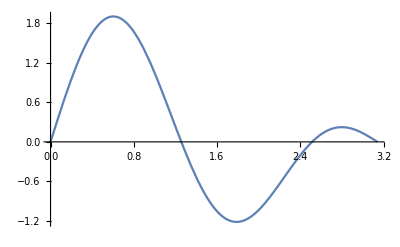

```mathematica
Plot[Sin[2x]+Sin[3x], {x, 0, Pi}]
```

```mathematica
Manipulate[
Plot[Sin[n1 x]+Sin[n2 x], {x, 0, Pi}],
{n1,1,10},
{n2, 15, 20}
]
```

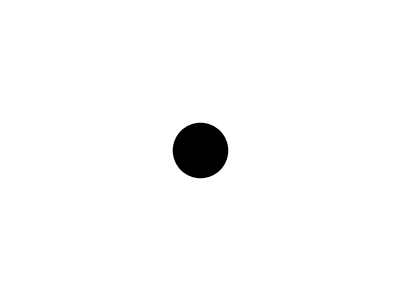

```mathematica
Graphics[{
PointSize[0.1],
Point[{0,0}]
}]
```

```mathematica
Manipulate[
Graphics[{
PointSize[0.1],
Point[pt]
},
PlotRange->1],
{pt, {-1,-1},{1,1}}
]
```